# Convolution

### Author

Eric W. Weisstein
August 18, 2008

This notebook downloaded from http://mathworld.wolfram.com/notebooks/IntegralTransforms/Convolution.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Convolution.html.

©2008 Wolfram Research, Inc. except for portions noted otherwise

### Code

```mathematica
MyConvolve[f_,g_,t_]:=Integrate[Function[t,f][τ]Function[t,g][t-τ],{τ,-∞,∞},GenerateConditions->False]
RectanglePi[x_]:=UnitStep[x+1/2]-UnitStep[x-1/2]
RectanglePi[x_,{a_,b_}]:=UnitStep[x-a]-UnitStep[x-b]
```

## Identities

### Convolve[f(x),g(x),x,t]==Convolve[g(x),f(x),x,t]

```mathematica
Convolve[f[x],g[x],x,t]-Convolve[g[x],f[x],x,t]
```

Convolve[f[x],g[x],x,t]-Convolve[g[x],f[x],x,t]

```mathematica
FullSimplify[%]
```

Convolve[f[x],g[x],x,t]-Convolve[g[x],f[x],x,t]

## Animations

```mathematica
<<Utilities`GIF`
```

Get::noopen: Cannot open Utilities`GIF`.

$Failed

### Rectangle

```mathematica
Convolve[.75RectanglePi[t],RectanglePi[t,{-1/4,1/4}]/2,t]
```

Convolve::argm: Convolve called with 3 arguments; 4 or more arguments are expected.

Convolve[0.75 (-UnitStep[-1/2+t]+UnitStep[1/2+t]),1/2 (-UnitStep[-1/4+t]+UnitStep[1/4+t]),t]

```mathematica
movie=With[
{h=Convolve[RectanglePi[t],.5RectanglePi[t,{-1/4,1/4}],t]},
Table[Show[
{
Plot[.5RectanglePi[t]RectanglePi[t-τ,{-1/4,1/4}],{t,-5,5},PlotPoints->100,ClippingStyle->False,Filling->Axis],
Plot[
{
RectanglePi[t],
.5RectanglePi[t-τ,{-1/4,1/4}],
h
},
{t,-2,2},
PlotStyle->{Red,Blue,Green},
ClippingStyle->False,
Exclusions->False
],
Graphics[{Green,Line[{{τ,-1},{τ,1}}],
{Red,Text[f,{0,.85},Background->White]},
{Blue,Text[g,{τ,.6},Background->White]}
}]
},
AxesLabel->{t,Star[f,g]},
Method->{"AxesInFront"->False},
PlotRange->{{-2,2},{-.1,1}}],
{τ,-2,2,.05}
]];
```

Convolve::argm: Convolve called with 3 arguments; 4 or more arguments are expected.

General::stop: Further output of Convolve::argm will be suppressed during this calculation.

```mathematica
ListAnimate[movie]
```

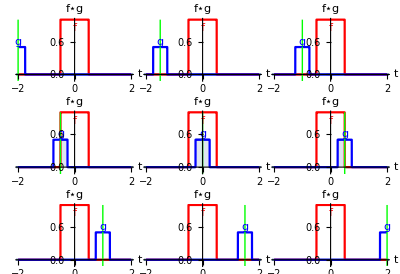

```mathematica
GraphicsGrid[Partition[Take[movie,{1,-1,10}],3],Spacings->{-40,10},ImageSize->400]
```

#### Animated GIF

```mathematica
Export[$GIFDirectory<>"convrect.gif",movie,"Interlaced"->True,"TransparentColor"->GrayLevel[1],AnimationRepetitions->∞,"DisplayDurations"->0.1]//Timing
```

StringJoin::string: String expected at position 1 in $GIFDirectory<>convrect.gif.

Export::chtype: First argument $GIFDirectory<>convrect.gif is not a valid file specification.

{0.111952,$Failed}

### Gaussian

```mathematica
movie=With[
{h=Convolve[Exp[-5t^2],Exp[-10t^2]/2,t]},
Table[Show[
{
Plot[Exp[-5t^2]Exp[-10(t-τ)^2]/2,{t,-5,5},PlotPoints->100,Filling->Axis,ClippingStyle->False],
Plot[
{
Exp[-5t^2],
Exp[-10(t-τ)^2]/2,
h
},
{t,-2,2},
ClippingStyle->False,
PlotStyle->{Red,Blue,Green}
],
Graphics[{Green,Line[{{τ,-1},{τ,1}}],
{Red,Text[f,{0,1.1},Background->White]},
{Blue,Text[g,{τ,.6},Background->White]}
}]
},
AxesLabel->{t,Star[f,g]},
Method->{"AxesInFront"->False},
PlotRange->{{-2,2},{-.1,1.1}}],{τ,-2,2,.05}
]];
```

Convolve::argm: Convolve called with 3 arguments; 4 or more arguments are expected.

General::stop: Further output of Convolve::argm will be suppressed during this calculation.

```mathematica
ListAnimate[movie]
```

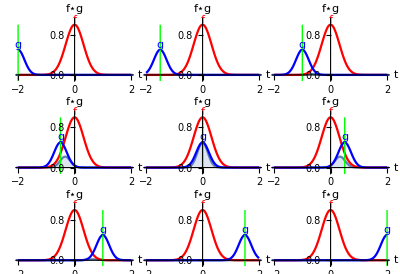

```mathematica
GraphicsGrid[Partition[Take[movie,{1,-1,10}],3],Spacings->{-40,10},ImageSize->400]
```

#### Animated GIF

```mathematica
Export[$GIFDirectory<>"convgaus.gif",movie,"Interlaced"->True,"TransparentColor"->GrayLevel[1],AnimationRepetitions->∞,"DisplayDurations"->0.1]//Timing
```

StringJoin::string: String expected at position 1 in $GIFDirectory<>convgaus.gif.

Export::chtype: First argument $GIFDirectory<>convgaus.gif is not a valid file specification.

{0.031013,$Failed}

## Analytic Cases

### Rectangle

#### V6

```mathematica
Convolve[a RectanglePi[t,{t1,t2}],b RectanglePi[t,{u1,u2}],t]
```

Convolve::argm: Convolve called with 3 arguments; 4 or more arguments are expected.

Convolve[a (UnitStep[t-t1]-UnitStep[t-t2]),b (UnitStep[t-u1]-UnitStep[t-u2]),t]

```mathematica
Convolve[a RectanglePi[t,{t1,t2}],b RectanglePi[t,{u1,u2}],t]%
```

Convolve::argm: Convolve called with 3 arguments; 4 or more arguments are expected.

Convolve[a (UnitStep[t-t1]-UnitStep[t-t2]),b (UnitStep[t-u1]-UnitStep[t-u2]),t]^2

#### V7

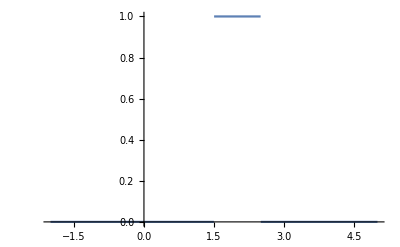

```mathematica
Plot[UnitBox[(x-2)/1],{x,-2,5}]
```

```mathematica
RectanglePi[t_,{t1_,t2_}]:=UnitBox[(t-Mean[{t1,t2}])/(t2-t1)]
```

```mathematica
Plot[RectanglePi[t,{3/2,5/2}],{t,-2,5}]
```

-Graphics-

```mathematica
TimeConstrained[Convolve[a RectanglePi[t,{t1,t2}],b RectanglePi[t,{u1,u2}],t,x],60]//Timing
```

{0.225603,a b (Piecewise[{{t1-t2, (t2<t1&&u2>t1-t2+u1&&t1+u1<x<t2+u2)||(t2<t1&&u2<-t1+t2+u1&&t1+u2<x≤t2+u1)}, {-t1+t2, (t2>t1&&u2>-t1+t2+u1&&t2+u1<x<t1+u2)||(t2>t1&&u2<t1-t2+u1&&t2+u2<x<t1+u1)}, {u1-u2, (t2>t1&&u2==t1-t2+u1&&x==t2+u2)||(t2>t1&&t1-t2+u1<u2<u1&&t1+u1≤x≤t2+u2)||(t2<t1&&u2==-t1+t2+u1&&x==t1+u2)||(t2<t1&&-t1+t2+u1<u2<u1&&t2+u1≤x≤t1+u2)}, {-u1+u2, (t2>t1&&u2==-t1+t2+u1&&x==t1+u2)||(t2>t1&&u1<u2<-t1+t2+u1&&t1+u2≤x≤t2+u1)||(t2<t1&&u2==t1-t2+u1&&x==t2+u2)||(t2<t1&&u1<u2<t1-t2+u1&&t2+u2≤x≤t1+u1)}, {t1+u1-x, (t2<t1&&u2==-t1+t2+u1&&t1+u2<x<t1+u1)||(t2<t1&&-t1+t2+u1<u2<u1&&t1+u2<x<t1+u1)||(t2<t1&&u2<-t1+t2+u1&&t2+u1<x<t1+u1)}, {t2+u1-x, (t2>t1&&u2==t1-t2+u1&&t2+u2<x<t2+u1)||(t2>t1&&t1-t2+u1<u2<u1&&t2+u2<x<t2+u1)||(t2>t1&&u2<t1-t2+u1&&t1+u1≤x<t2+u1)}, {t1+u2-x, (t2<t1&&u2==t1-t2+u1&&t2+u2<x<t1+u2)||(t2<t1&&u2>t1-t2+u1&&t2+u2≤x<t1+u2)||(t2<t1&&u1<u2<t1-t2+u1&&t1+u1<x<t1+u2)}, {t2+u2-x, (t2>t1&&u2==-t1+t2+u1&&t1+u2<x<t2+u2)||(t2>t1&&u2>-t1+t2+u1&&t1+u2≤x<t2+u2)||(t2>t1&&u1<u2<-t1+t2+u1&&t2+u1<x<t2+u2)}, {-t1-u1+x, (t2>t1&&u2==-t1+t2+u1&&t1+u1<x<t1+u2)||(t2>t1&&u2>-t1+t2+u1&&t1+u1<x≤t2+u1)||(t2>t1&&u1<u2<-t1+t2+u1&&t1+u1<x<t1+u2)}, {-t2-u1+x, (t2<t1&&u2==t1-t2+u1&&t2+u1<x<t2+u2)||(t2<t1&&u2>t1-t2+u1&&t2+u1<x≤t1+u1)||(t2<t1&&u1<u2<t1-t2+u1&&t2+u1<x<t2+u2)}, {-t1-u2+x, (t2>t1&&u2==t1-t2+u1&&t1+u2<x<t2+u2)||(t2>t1&&t1-t2+u1<u2<u1&&t1+u2<x<t1+u1)||(t2>t1&&u2<t1-t2+u1&&t1+u2<x≤t2+u2)}, {-t2-u2+x, (t2<t1&&u2==-t1+t2+u1&&t2+u2<x<t1+u2)||(t2<t1&&-t1+t2+u1<u2<u1&&t2+u2<x<t2+u1)||(t2<t1&&u2<-t1+t2+u1&&t2+u2<x≤t1+u2)}, {0, True}}])}

```mathematica
TimeConstrained[Convolve[a RectanglePi[t,{t1,t2}],b RectanglePi[t,{u1,u2}],t,x,Assumptions->(a|b|t1|t2|u1|u2)∈Reals],60]//Timing
```

{0.119598,a b (Piecewise[{{t1-t2, (t2<t1&&u2>t1-t2+u1&&t1+u1<x<t2+u2)||(t2<t1&&u2<-t1+t2+u1&&t1+u2<x≤t2+u1)}, {-t1+t2, (t2>t1&&u2>-t1+t2+u1&&t2+u1<x<t1+u2)||(t2>t1&&u2<t1-t2+u1&&t2+u2<x<t1+u1)}, {u1-u2, (t2>t1&&u2==t1-t2+u1&&x==t2+u2)||(t2>t1&&t1-t2+u1<u2<u1&&t1+u1≤x≤t2+u2)||(t2<t1&&u2==-t1+t2+u1&&x==t1+u2)||(t2<t1&&-t1+t2+u1<u2<u1&&t2+u1≤x≤t1+u2)}, {-u1+u2, (t2>t1&&u2==-t1+t2+u1&&x==t1+u2)||(t2>t1&&u1<u2<-t1+t2+u1&&t1+u2≤x≤t2+u1)||(t2<t1&&u2==t1-t2+u1&&x==t2+u2)||(t2<t1&&u1<u2<t1-t2+u1&&t2+u2≤x≤t1+u1)}, {t1+u1-x, (t2<t1&&u2==-t1+t2+u1&&t1+u2<x<t1+u1)||(t2<t1&&-t1+t2+u1<u2<u1&&t1+u2<x<t1+u1)||(t2<t1&&u2<-t1+t2+u1&&t2+u1<x<t1+u1)}, {t2+u1-x, (t2>t1&&u2==t1-t2+u1&&t2+u2<x<t2+u1)||(t2>t1&&t1-t2+u1<u2<u1&&t2+u2<x<t2+u1)||(t2>t1&&u2<t1-t2+u1&&t1+u1≤x<t2+u1)}, {t1+u2-x, (t2<t1&&u2==t1-t2+u1&&t2+u2<x<t1+u2)||(t2<t1&&u2>t1-t2+u1&&t2+u2≤x<t1+u2)||(t2<t1&&u1<u2<t1-t2+u1&&t1+u1<x<t1+u2)}, {t2+u2-x, (t2>t1&&u2==-t1+t2+u1&&t1+u2<x<t2+u2)||(t2>t1&&u2>-t1+t2+u1&&t1+u2≤x<t2+u2)||(t2>t1&&u1<u2<-t1+t2+u1&&t2+u1<x<t2+u2)}, {-t1-u1+x, (t2>t1&&u2==-t1+t2+u1&&t1+u1<x<t1+u2)||(t2>t1&&u2>-t1+t2+u1&&t1+u1<x≤t2+u1)||(t2>t1&&u1<u2<-t1+t2+u1&&t1+u1<x<t1+u2)}, {-t2-u1+x, (t2<t1&&u2==t1-t2+u1&&t2+u1<x<t2+u2)||(t2<t1&&u2>t1-t2+u1&&t2+u1<x≤t1+u1)||(t2<t1&&u1<u2<t1-t2+u1&&t2+u1<x<t2+u2)}, {-t1-u2+x, (t2>t1&&u2==t1-t2+u1&&t1+u2<x<t2+u2)||(t2>t1&&t1-t2+u1<u2<u1&&t1+u2<x<t1+u1)||(t2>t1&&u2<t1-t2+u1&&t1+u2<x≤t2+u2)}, {-t2-u2+x, (t2<t1&&u2==-t1+t2+u1&&t2+u2<x<t1+u2)||(t2<t1&&-t1+t2+u1<u2<u1&&t2+u2<x<t2+u1)||(t2<t1&&u2<-t1+t2+u1&&t2+u2<x≤t1+u2)}, {0, True}}])}

#### V7

### Gaussian

#### V6

```mathematica
Convolve[a Exp[-(t-Subscript[μ, 1])^2/(2 Subscript[σ, 1]^2)]/Subscript[σ, 1]/Sqrt[2π],b Exp[-(t-Subscript[μ, 2])^2/(2 Subscript[σ, 2]^2)]/Subscript[σ, 2]/Sqrt[2π],t]
```

Convolve::argm: Convolve called with 3 arguments; 4 or more arguments are expected.

Convolve[(a ⅇ^(-(t-μ_1)^2/(2 σ_1^2)))/(√(2 π) σ_1),(b ⅇ^(-(t-μ_2)^2/(2 σ_2^2)))/(√(2 π) σ_2),t]

```mathematica
FullSimplify[%,Subscript[σ, 1]>0&&Subscript[σ, 2]>0]
```

Convolve[(a ⅇ^(-(t-μ_1)^2/(2 σ_1^2)))/(√(2 π) σ_1),(b ⅇ^(-(t-μ_2)^2/(2 σ_2^2)))/(√(2 π) σ_2),t]

```mathematica
FullSimplify[ √((1/Subscript[σ, 1]^2+1/Subscript[σ, 2]^2)Subscript[σ, 1]^2 Subscript[σ, 2]^2)]
```

√(σ_1^2+σ_2^2)

(ⅇ^(-(t-(μ_1+μ_2))^2/(2 (σ_1^2+σ_2^2))))/(√(2 π (σ_1^2+σ_2^2)))

#### V7

```mathematica
Convolve[a Exp[-(t-Subscript[μ, 1])^2/(2 Subscript[σ, 1]^2)]/Subscript[σ, 1]/Sqrt[2π],b Exp[-(t-Subscript[μ, 2])^2/(2 Subscript[σ, 2]^2)]/Subscript[σ, 2]/Sqrt[2π],t,x]
```

(a b ⅇ^(-(-x+μ_1+μ_2)^2/(2 (σ_1^2+σ_2^2))))/(√(2 π) σ_1 √(1/σ_1^2+1/σ_2^2) σ_2)